## 8.4 Other bifurcations of periodic orbits

#### Saddle-node coalescence of limit cycles

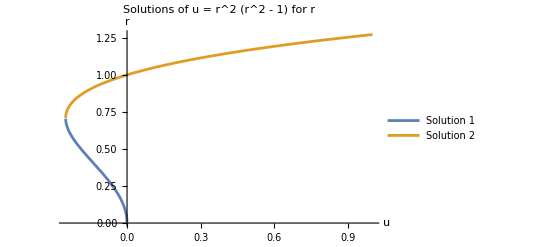

```mathematica
sol = Solve[u == r^2 (r^2 - 1), r];
sol1 = sol[[1]];
sol2 = sol[[2]];
sol3 = sol[[3]];
sol4 = sol[[4]];

Plot[{(*r /. sol1,*) r /. sol2, (*r /. sol3,*) r /. sol4}, {u, -1, 1}, 
  PlotRange -> All, 
  AxesLabel -> {"u", "r"}, 
  PlotLegends -> {"Solution 1", "Solution 2", "Solution 3", "Solution 4"}, 
  PlotLabel -> "Solutions of u = r^2 (r^2 - 1) for r"]
```

#### SNIPER - saddle node infinite period bifurcation on a cycle

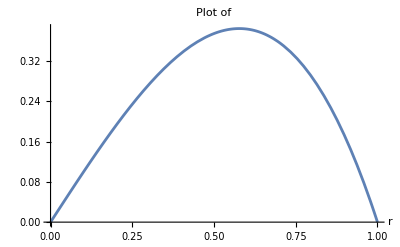

```mathematica
Plot[r (1 - r^2), {r, 0, 1}, PlotRange -> All, AxesLabel -> {"r", ""}, 
    PlotLabel -> "Plot of "]
```

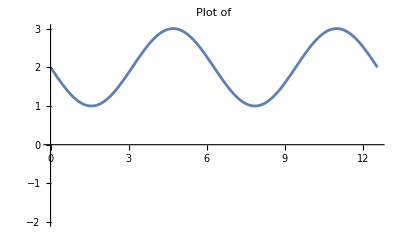

```mathematica
w = 2;
Plot[w - Sin[theta], {theta, 0, 4*Pi}, PlotRange -> {{0, 4*Pi}, {-2, 3}}, AxesLabel -> {"", ""}, 
    PlotLabel -> "Plot of "]
```

## 7. Limit cycles

### A SIMPLE LIMIT CYCLE , Which has a fixed point at r = 0 and one where r = 1.

```mathematica
ClearAll["Global`*"]

(* Define the differential equation *)
eq = r'[t] == r[t] (1 - r[t]^2);

(* Numerical solution with NDSolve and different initial conditions *)
sol1 = NDSolve[{eq, r[0] == 0.000001}, r, {t, 0, 100}];
sol2 = NDSolve[{eq, r[0] == 1.1}, r, {t, 0, 1000}];

(* Parametric plot of the numerical solutions *)
plot1 = ParametricPlot[Evaluate[{r[t], r'[t]} /. sol1], {t, 0, 100}, AspectRatio -> 1, PlotRange -> {{0, 2}, {-1,1}}, AxesLabel -> {"r", "r'"}];
plot2 = ParametricPlot[Evaluate[{r[t], r'[t]} /. sol2], {t, 0, 1000}, AspectRatio -> 1, PlotRange -> {{0, 2}, {-1,1}}, AxesLabel -> {"r", "r'"}];
(*plot2 = ParametricPlot[Evaluate[{r[t], r'[t]} /. sol2], {t, 0, 1000}, AspectRatio -> 1, PlotRange -> {{0.9,1.3},All}, AxesLabel -> {"r", "r'"}];*)

(* Show both plots *)
Show[plot1,plot2];
```

Maybe I am only imagining this but, i have noticed that the fixed point at  has no problem with values close to 0, while the other fixed point does not “like” to have the initial value close to r = 1. What I mean is that since the fixed point at  is an unstable one, the same off set from 0 (e.g. 0.000001) with tMax=10  goes much further than 1.000001 with  tMax=10. Weird.

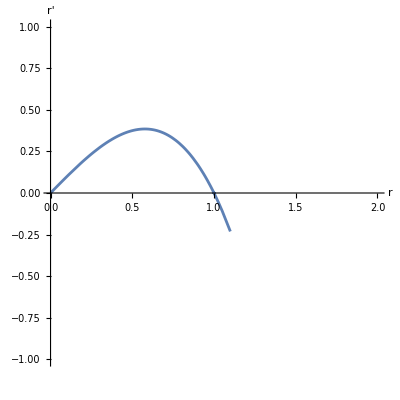

```mathematica
ClearAll["Global`*"]

tMax = 1000;
tMaxPlot = 10;

(* Define the system of differential equations in polar coordinates *)
eq1 = r'[t] == r[t] (1 - r[t]^2);
eq2 = θ'[t] == 1;

(* Initial conditions *)
initialConditions = {r[0] == 0.001, θ[0] == 0};
initialConditions2 = {r[0] == 1.4, θ[0] == 0};
initialConditions3 = {r[0] == -0.001, θ[0] == 0};
initialConditions4 = {r[0] == -1.1, θ[0] == 0};

(* Solve the system *)
sol1 = NDSolve[{eq1, eq2, initialConditions}, {r, θ}, {t, 0, tMax}];
sol2 = NDSolve[{eq1, eq2, initialConditions2}, {r, θ}, {t, 0, tMax}];
sol3 = NDSolve[{eq1, eq2, initialConditions3}, {r, θ}, {t, 0, tMax}];
sol4 = NDSolve[{eq1, eq2, initialConditions4}, {r, θ}, {t, 0, tMax}];

(* Transform polar coordinates to Cartesian coordinates *)
r1[t_] = r[t] /. sol1[[1]];
θ1[t_] = θ[t] /. sol1[[1]];

r2[t_] = r[t] /. sol2[[1]];
θ2[t_] = θ[t] /. sol2[[1]];

r3[t_] = r[t] /. sol3[[1]];
θ3[t_] = θ[t] /. sol3[[1]];

r4[t_] = r[t] /. sol4[[1]];
θ4[t_] = θ[t] /. sol4[[1]];

x1[t_] := r1[t] Cos[θ1[t]];
y1[t_] := r1[t] Sin[θ1[t]];

x2[t_] := r2[t] Cos[θ2[t]];
y2[t_] := r2[t] Sin[θ2[t]];

x3[t_] := r3[t] Cos[θ3[t]];
y3[t_] := r3[t] Sin[θ3[t]];

x4[t_] := r4[t] Cos[θ4[t]];
y4[t_] := r4[t] Sin[θ4[t]];

(* Function to plot arrows along the trajectory *)
arrowPlot[{x_, y_}, {vx_, vy_}, scale_] := {Arrowheads[0.02], Arrow[{{x, y}, {x + scale vx, y + scale vy}}]}

(* Plot the phase plane with arrows *)
ParametricPlot[{{x1[t], y1[t]}, {x2[t], y2[t]}, {x3[t], y3[t]}, {x4[t], y4[t]}}, {t, 0, tMaxPlot}, 
 AspectRatio -> 1,
 PlotRange -> All,
 AxesLabel -> {"x", "y"},
 PlotLabel -> "Phase Plane Plot",
 Epilog -> {Red, PointSize[Large], Point[{0, 0}], Circle[{0, 0}, 1, {0, 2 Pi}]}
 ];
```

This is a phase plane show an unstable fixed point in at the origine (red) and a stable limit cycle (red) around with radius = 1.

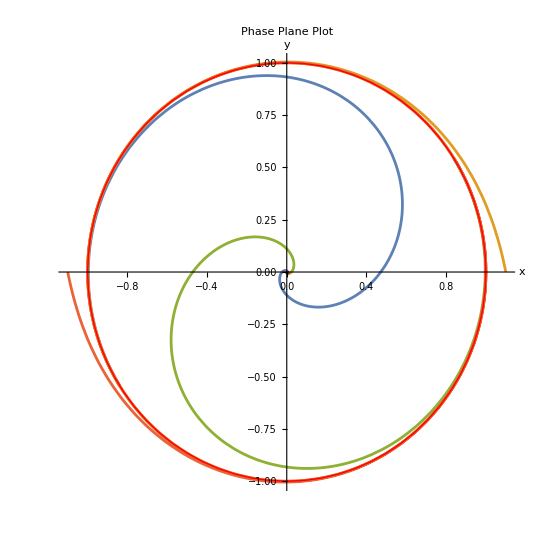

```mathematica
tMaxPlot1 = 20;

(* Plot x(t) for initialConditions2 *)
Plot[x1[t], {t, 0, tMaxPlot1}, 
  AxesLabel -> {"t", "x(t)"},
  PlotLabel -> "x(t) for initialConditions1",
  PlotStyle -> Blue
];
```

In this plot the behaviour the x coordinate depending on t of a trajectory from inside (= I.C. 1) are shown. One can see that there is the x-coordinate come into a sinusoidal motion after some time.

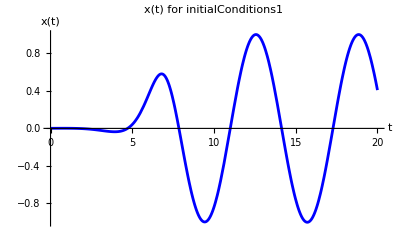

In this plot the behaviour the x coordinate depending on t of a trajectory from outside (= I.C. 2) are shown. One can see that there is the x-coordinate come into a sinusoidal motion after some time.

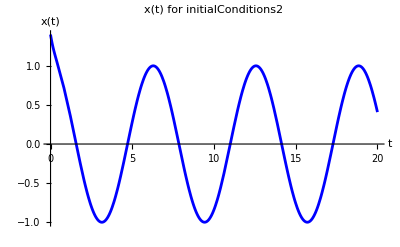

### VAN DER POOL OSCILLATOR Is plotted using one second order differential equation. System: with and

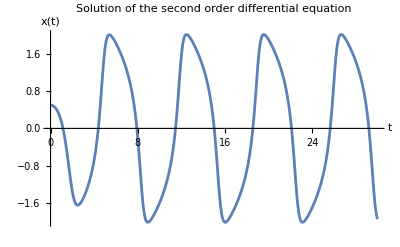

```mathematica
ClearAll["Global`*"]

(*Paramters*)
tMax=30;
mu = 1.5;

(* Define the ODE and initial conditions *)
ode = {x''[t] + mu (x[t]^2 - 1) x'[t] + x[t] == 0, x[0] == 0.5, x'[0] == 0};


(* Numerically solve the ODE *)
sol = NDSolve[ode, x, {t, 0, tMax}];

(* Plot the solution *)
Plot[Evaluate[x[t] /. sol], {t, 0, tMax}, PlotRange -> All, 
  AxesLabel -> {"t", "x(t)"},
  PlotLabel -> "Solution of the second order differential equation"
]
```

Here the example of the VAN DER POOL OSCILLATOR is plotted using two first order differential equations. 
The system looks like:
	
	
with  and

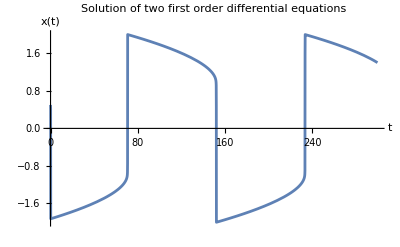

```mathematica
ClearAll["Global`*"]

tMax = 300;
mu = 100;

eqns = {
  u'[t] == v[t],
  v'[t] == -mu (u[t]^2 - 1) v[t] - u[t],
  u[0] == 0.5,
  v[0] == 0
};

sol = NDSolve[eqns, {u, v}, {t, 0, tMax}];

Plot[u[t] /. sol, {t, 0, tMax}, 
  AxesLabel -> {"t", "x(t)"},
  FrameLabel -> {"t", "u(t)"}, 
  PlotLabel -> "Solution of two first order differential equations"]
```

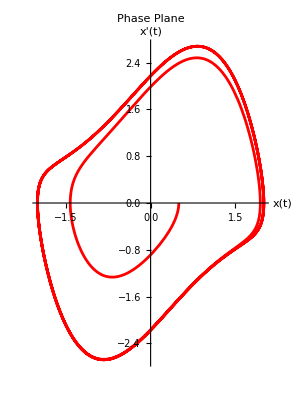

```mathematica
ClearAll["Global`*"]
mu = 1;
initialConditions = {x[0] == 0.5, x'[0] == 0};
tMax = 30;

(* Define the ODE and initial conditions *)
ode = {x''[t] + mu (x[t]^2 - 1) x'[t] + x[t] == 0, initialConditions};

(* Numerically solve the ODE *)
sol = NDSolve[ode, {x, x'}, {t, 0, tMax}];

(* Extract the solution for plotting *)
{xSol, xPrimeSol} = {x[t], x'[t]} /. sol[[1]];

(* Plot the phase plane with arrows and increased resolution *)
ParametricPlot[{xSol, xPrimeSol}, {t, 0, tMax}, 
  PlotStyle -> Red, AxesLabel -> {"x(t)", "x'(t)"}, 
  PlotLabel -> "Phase Plane",
  PlotRange -> Full,
  PlotPoints -> 200, (* You can adjust this value *)
  MaxRecursion -> 6 (* You can adjust this value *)
]
```

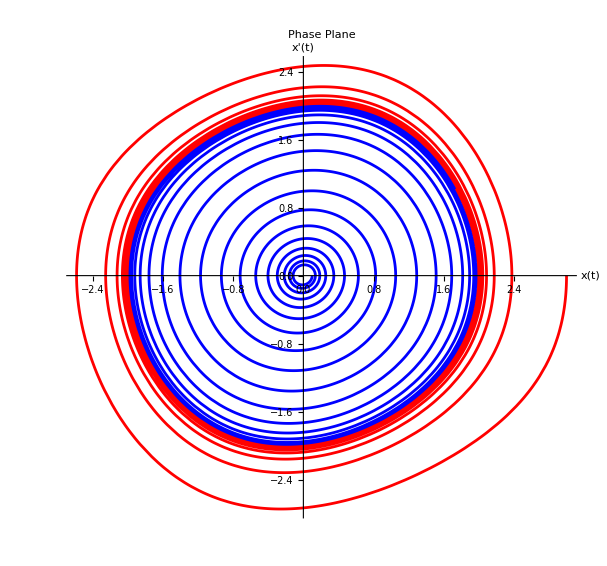

```mathematica
ClearAll["Global`*"]
mu = 0.1;
initialConditionsOutside = {x[0] == 3, x'[0] == 0};
initialConditionsInside = {x[0] == 0.1, x'[0] == 0};
tMax = 100;

(* Define the ODE and initial conditions *)
odeOutside = {x''[t] + mu (x[t]^2 - 1) x'[t] + x[t] == 0, initialConditionsOutside};
odeInside = {x''[t] + mu (x[t]^2 - 1) x'[t] + x[t] == 0, initialConditionsInside};

(* Numerically solve the ODE *)
solOutside = NDSolve[odeOutside, {x, x'}, {t, 0, tMax}];
solInside = NDSolve[odeInside, {x, x'}, {t, 0, tMax}];

(* Extract the solution for plotting *)
{xSol, xPrimeSol} = {x[t], x'[t]} /. solOutside[[1]];
{xSol2, xPrimeSol2} = {x[t], x'[t]} /. solInside[[1]];

(* Plot the phase plane with arrows *)
ParametricPlot[{{xSol, xPrimeSol}, {xSol2, xPrimeSol2}}, {t, 0, tMax}, 
  PlotStyle -> {Red, Blue}, AxesLabel -> {"x(t)", "x'(t)"}, 
  PlotLabel -> "Phase Plane",
  PlotRange -> Full,
  PlotPoints -> 200, (* Adjust this value to increase the points that will be plotted, the higher the better *)
  MaxRecursion -> 6 (* the higher the better *)
]
```

## Rössler attractor

```mathematica
ClearAll["Global`*"]

(* Rössler variables *)
a = 2;
b = 2;
c = 5.7;

(* Differential equation system *)
Equation1 = x'[t] == -y[t] - x[t];
Equation2 = y'[t] == x[t] + a*y[t];
Equation3 = z'[t] == b+z[t]*(x[t]-c);
System = {Equation1, Equation2, Equation3};

(* Fixed points of the differential equation system *)
FixedPoint1 = {(c+Sqrt[c^2-4*a*b])/2, (-c-Sqrt[c^2-4*a*b])/(2*a), (c+Sqrt[c^2-4*a*b])/(2*a)};
FixedPoint2 = {(c-Sqrt[c^2-4*a*b])/2, (-c+Sqrt[c^2-4*a*b])/(2*a), (c-Sqrt[c^2-4*a*b])/(2*a)};

(* Parameters for the plot *)
eta = 0.1;
t0 = 0;
tMax = 20;
tZeroPlot = 1;

(* Starting point of the trajectory (distance from fixed points handled via eta) *)
StartingPoint = {x[0] == FixedPoint1[[1]] + eta, y[0] == FixedPoint1[[2]] - eta, z[0] == FixedPoint1[[3]] - eta};
(*StartingPoint = {x[0] == + eta, y[0] == + eta, z[0] == - eta};*)

Solution = NDSolve[{System, StartingPoint}, {x, y, z}, {t, t0, tMax}, MaxSteps -> Infinity];


(* Plotting *)
plot = ParametricPlot3D[Evaluate[{x[t], y[t], z[t]} /. Solution], {t, t0, tMax}, 
(*PlotPoints -> 1000,*)
PlotLabel -> Style["(x,z)-plot", 
FontSize -> 18],
PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]], 
ColorFunction -> (ColorData["SolarColors", #4] &), 
PlotRange -> All, 
Axes -> False];

fixedPoints = Graphics3D[{Blue, PointSize[0.02], Point[{FixedPoint1, FixedPoint2}]}];
Show[plot,fixedPoints]


(*Toying around*)
(*fixedPoints = Graphics3D[{Blue, PointSize[0.02], Point[{FixedPoint1,FixedPoint2,FixedPoint3}]}];
fixedPoints1 = Graphics3D[{Blue, PointSize[0.02], Point[{0,0,0}]}];
Show[plot,fixedPoints]*)
```

General::munfl: 1/(4.89507×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.79223×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.85408×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

ReplaceAll::reps: {Solution} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-